## Brandvain and Coop. Sperm dependent female meiotic drive

Model 1. Female drive depends on sperm haplotype (single pleitropic locus)

The B allele is transmited with probability, d, in heterozygous females when fertilized by B-bearing sperm. 
x represents the deviation from Hardy - Weinberg Equilibrium

## Setup

```mathematica
(*Allele and Genotype frequencies*)
ClearAll["Global`*"]
fA=1-fB;
fAA = fA^2+fA fB x;
fAB = 2fA fB(1-x);
fBB= fB^2+fA fB x;
```

#### Drive

```mathematica
(*Genotype frequencies after drive*)
Subscript[fAA, Drive]=FullSimplify[fA(fAA+fAB/2)];
Subscript[fAB, Drive] =FullSimplify[fB(fAA+fAB*(1-d))+fA(fAB/2+fBB)];
Subscript[fBB, Drive] =FullSimplify[fB(fAB d+fBB )];
```

#### Selection

```mathematica
wAA=1;wAB=1-hs;wBB=1-s; (*genotypic fitnesses*)
W̄=FullSimplify[Subscript[fAA, Drive] wAA+Subscript[fAB, Drive] wAB+Subscript[fBB, Drive] wBB];(*mean fitness*)
Subscript[fAA, Sel]=FullSimplify[(Subscript[fAA, Drive]*wAA)/W̄];
Subscript[fAB, Sel]=FullSimplify[(Subscript[fAB, Drive]*wAB)/W̄];
Subscript[fBB, Sel]=FullSimplify[(Subscript[fBB, Drive] wBB)/W̄];
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+Subscript[fAB, Sel]/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+Subscript[fAB, Sel]/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
```

## Analysis

Note, we assume no deviation from Hardy-Weinberg [i.e. x=0] for all analytical results, and therefore these answers are approximations. In the supplamentary material we show thats results of exact recursions are remarkably consistant from these approximate analystical solutions.

### Assuming the cost of drive is fully recessive [i.e. hs is zero]

#### Invasion

```mathematica
ΔfBinvade=(FullSimplify[ΔfB/.hs->0/.x->0]/fB^2/.fB->0)
```

1/2 (-1+d (2-4 s))

```mathematica
spermDepReceesiveInvade =Solve[ΔfBinvade==0,s]
```

{{s→(-1+2 d)/(4 d)}}

```mathematica
plotInvasion4spermDepRecessive=Plot[s/.spermDepReceesiveInvade [[1]],{d,.5,1},PlotStyle->{Black,Thick}];
```

```mathematica
plotRelChange4RarespermDepRecessive=ContourPlot[{ΔfBinvade},{d,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],FrameLabel->{"d (drive)","s (selection)"},PlotLabel->"Invasion of recessive sperm dependent driver"];
```

```mathematica
Show[plotRelChange4RarespermDepRecessive,plotInvasion4spermDepRecessive]
```

-Graphics-

#### Fixation

```mathematica
ΔfBfix=FullSimplify[FullSimplify[ΔfB/.hs->0/.x->0]/fA]/.fB->1
```

(-1+2 d-2 s)/(2-2 s)

```mathematica
spermDepReceesiveFix =Solve[ΔfBfix==0,s]
```

{{s→1/2 (-1+2 d)}}

```mathematica
(s/.spermDepReceesiveFix [[1]])
```

1/2 (-1+2 d)

```mathematica
plotFixation4spermDepRecessive=Plot[s/.spermDepReceesiveFix  [[1]],{d,.5,1},PlotStyle->{Red,Thick}];
```

```mathematica
(*Note we artificially rescaled z to be -.1 for all negative values*)
plotRelChange4CommonSpermDepRecessive=ContourPlot[If[s>(s/.spermDepReceesiveFix [[1]]),-.1,ΔfBfix],{d,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],FrameLabel->{"d (dirve)","s (selection)"},PlotLabel->"Fixation of recessive sperm dependent driver"];
```

```mathematica
Show[plotRelChange4CommonSpermDepRecessive,plotFixation4spermDepRecessive]
```

-Graphics-

#### Bistability Point

```mathematica
FBbistabSpermDepReceesive=Solve[FullSimplify[ΔfB/.hs->0/.x->0]==0,fB][[4]]
```

{fB→(1-2 d+4 d s)/(-2 s+4 d s)}

```mathematica
bistab=ContourPlot[(If[fB<0,0,If[fB>1,1,fB]])/.FBbistabSpermDepReceesive,{d,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],FrameLabel->{"d (dirve)","s (selection)"},PlotLabel->"Threshold frequency for fixation of recessive self-promoting driver"];
```

```mathematica
Show[bistab,plotFixation4spermDepRecessive,plotInvasion4spermDepRecessive]
```

-Graphics-

### Assuming the cost of drive is not fully recessive [i.e. hs is nonzero]

#### Invasion

Note  with any heterozgous cost (i.e. hs > 0) a self - promoting driver cannot invade

```mathematica
FullSimplify[FullSimplify[ΔfB/.x->0]/fB]/.fB->0
```

-hs

#### Fixation

```mathematica
ΔfBfix=FullSimplify[FullSimplify[FullSimplify[ΔfB/.x->0]/fA]/.fB->1]
```

(1+2 d (-1+hs)-3 hs+2 s)/(2 (-1+s))

```mathematica
spermDepNotReceesiveFix =Solve[ΔfBfix==0,s]
```

{{s→1/2 (-1+2 d)}}

```mathematica
spermDepAddFix =Solve[ΔfBfix==0/.hs->s/2,s]
```

{{s→1/2 (-1+2 d)}}

```mathematica
plotspermDepAddFix =Plot[s/.spermDepAddReceesiveFix ,{d,.5,1},PlotStyle->{Red,Thick}];
```

#### Bistability Point

```mathematica
FBbistabSpermDepNotReceesive=Solve[FullSimplify[ΔfB/.x->0]==0,fB][[3]]
```

{fB→(-1+2 d+3 hs+2 d hs-4 d s-√(-8 hs (-2 hs+4 d hs+2 s-4 d s)+(1-2 d-3 hs-2 d hs+4 d s)^2))/(2 (-2 hs+4 d hs+2 s-4 d s))}

An Example of a non - recessive driver [Assuming additivity]

```mathematica
bistab=ContourPlot[(If[fB<0,0,If[fB>1,1,fB]])/.FBbistabSpermDepNotReceesive/.hs->(s/2),{d,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],FrameLabel->{"d (dirve)","s (selection)"},PlotLabel->"Threshold frequency for fixation of recessive self-promoting driver"];
```

```mathematica
Show[bistab,plotspermDepAddFix]
```

-Graphics-

Model 2. Female drive depends on male genotype (single pleitropic locus)

The B allele is transmited with probability, d and dh, in heterozygous females when fertilized BB and AB males, respectively.  
x represents the deviation from Hardy - Weinberg Equilibrium

## Setup

```mathematica
(*Allele and Genotype frequencies*)
ClearAll["Global`*"]
fA=1-fB;
fAA = fA^2+fA fB x;
fAB = 2fA fB(1-x);
fBB= fB^2+fA fB x;
```

### Drive

```mathematica
(*Genotype frequencies after drive*)
Subscript[fAA, Drive]=FullSimplify[fAA(fAA+fAB/2)+fAB(fAA/2+fAB(1-dh)/2)];
Subscript[fAB, Drive] =FullSimplify[fAA(fAB/2+fBB)+fAB(fAA/2+fAB/2+fBB(1-d))+fBB(fAA+fAB/2)];
Subscript[fBB, Drive] =FullSimplify[fAB(fAB dh/2+fBB d)+fBB(fAB/2+fBB)];
```

### Selection

```mathematica
wAA=1;wAB=1-hs;wBB=1-s; (*genotypic fitnesses*)
W̄=FullSimplify[Subscript[fAA, Drive] wAA+Subscript[fAB, Drive] wAB+Subscript[fBB, Drive] wBB];(*mean fitness*)
Subscript[fAA, Sel]=FullSimplify[(Subscript[fAA, Drive]*wAA)/W̄];
Subscript[fAB, Sel]=FullSimplify[(Subscript[fAB, Drive]*wAB)/W̄];
Subscript[fBB, Sel]=FullSimplify[(Subscript[fBB, Drive] wBB)/W̄];
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+Subscript[fAB, Sel]/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+Subscript[fAB, Sel]/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
```

### Analysis

#### Analytical example - recessive fitness cost

Invasion

```mathematica
invasion4maleDepRecessive=Solve[((FullSimplify[(ΔfB/.x->0/.hs->0)]/fB^2)/.fB->0)==0,s]
```

{{s→(-1+2 dh)/(2 dh)}}

```mathematica
plotiInvasion4maleDepRecessive=Plot[s /. invasion4maleDepRecessive /. dh -> d, {d, .5, 1}, PlotStyle -> {Black, Thick}];
```

Fixation

```mathematica
fixation4maleDepRecessive=Solve[(FullSimplify[(FullSimplify[(ΔfB/.x->0/.hs->0)/fA]/.fB->1)])==0,s]
```

{{s→1/2 (-1+2 d)}}

```mathematica
plotFixation4maleDepRecessive=Plot[s /. fixation4maleDepRecessive /. dh -> d, {d, .5, 1}, PlotStyle -> {Red, Thick}];
```

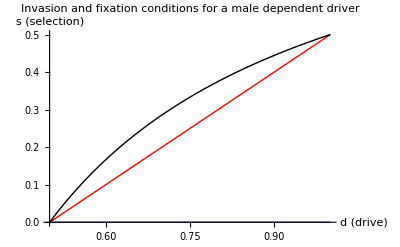

```mathematica
Show[Plot[0,{d,0.5,1},AxesLabel->{"d (drive)","s (selection)"},PlotRange->{{.5,1},{0,.5}}, PlotLabel->"Invasion and fixation conditions for a male dependent driver"],plotFixation4maleDepRecessive,plotiInvasion4maleDepRecessive]
```

Bistability

```mathematica
FBbistabMaleepReceesive=Solve[FullSimplify[ΔfB/.x->0/.hs->0/.dh->d]==0,fB][[4]]
```

{fB→(2 (1-2 d+2 d s))/((-1+2 d) (-1+2 s))}

```mathematica
bistab=ContourPlot[ (If[fB<0,0,If[fB>1,1,fB]])/.FBbistabMaleepReceesive,{d,0.5,1},{s,0,.5},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],FrameLabel->{"d (drive) assuming dhet=dhom=d","s (selection, assuming recessive fitness cost)"}];
```

```mathematica
Show[bistab,plotiInvasion4maleDepRecessive,plotFixation4maleDepRecessive]
```

-Graphics-

Model 3. Female drive depends on sperm haplotype (two tightly linked loci)

We have one locus with two alleles, A (non-driving) and B (traditional driver), as well as a tightly linked locus where one allele  modifies drive. Assuming no recombination this functions as a third allele, C. 
When C increases drive in heterozgous females it fertilizes, it is a drive enhancer (the B+ allele in our ms).
When C decreases drive in heterozgous females it fertilizes, it is a drive suppressor (the B- allele in our ms).

## Setup

```mathematica
ClearAll["Global`*"]
fA=.
fAA=.
fAB=.
fAC=.
fBB=.
fBC=.
fCC=.
minormod = {d1->d0+ϵ} (*assuming the sperm acting modifier additively increases drive by epsilon*);
SUMTOONE ={ fA->1-(fB+fC)};
HWE={fAA->fA^2,fAB->2fA fB,fAC->2fA fC,fBB -> fB^2, fBC->2fB fC,fCC->fC^2};
GENOFREQS = {fA->fAA+fAB/2+fAC/2,fB->fBB+fAB/2+fBC/2,fC->fCC+fBC/2+fBC/2};
```

### Drive

```mathematica
(*Here we caculate all genotypes after drive. For book-keeping purposes we distinguish between reciprocal homozygotes, but remove this distinction belowsum them below*)
```

```mathematica
AAn=FullSimplify[fAA*fAA*1+fAA*fAB*1/2+fAA*fAC*1/2+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*(1-d0)+fAB*fAB*(1-d0)/2+fAB*fAC*(1-d0)/2+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*(1-d0)+fAC*fAB*(1-d0)/2+fAC*fAC*(1-d0)/2+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
ABn=FullSimplify[fAA*fAA*0+fAA*fAB*1/2+fAA*fAC*0+fAA*fBB*1+fAA*fBC*1/2+fAA*fCC*0+fAB*fAA*0+fAB*fAB*(1-d0)/2+fAB*fAC*0+fAB*fBB*(1-d0)+fAB*fBC*(1-d0)/2+fAB*fCC*0+fAC*fAA*0+fAC*fAB*(1-d0)/2+fAC*fAC*0+fAC*fBB*(1-d0)+fAC*fBC*(1-d0)/2+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
ACn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*1/2+fAA*fBB*0+fAA*fBC*1/2+fAA*fCC*1+fAB*fAA*0+fAB*fAB*0+fAB*fAC*(1-d1)/2+fAB*fBB*0+fAB*fBC*(1-d1)/2+fAB*fCC*(1-d1)+fAC*fAA*0+fAC*fAB*0+fAC*fAC*(1-d1)/2+fAC*fBB*0+fAC*fBC*(1-d1)/2+fAC*fCC*(1-d1)+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*0+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BAn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*d0+fAB*fAB*d0/2+fAB*fAC*d0/2+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*1+fBB*fAB*1/2+fBB*fAC*1/2+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*1/2+fBC*fAB*1/4+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BBn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*d0/2+fAB*fAC*0+fAB*fBB*d0+fAB*fBC*d0/2+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*1/2+fBB*fAC*0+fBB*fBB*1+fBB*fBC*1/2+fBB*fCC*0+fBC*fAA*0+fBC*fAB*1/4+fBC*fAC*0+fBC*fBB*1/2+fBC*fBC*1/4+fBC*fCC*0+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
BCn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*(d1)/2+fAB*fBB*0+fAB*fBC*(d1)/2+fAB*fCC*d1+fAC*fAA*0+fAC*fAB*0+fAC*fAC*0+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*1/2+fBB*fBB*0+fBB*fBC*1/2+fBB*fCC*1+fBC*fAA*0+fBC*fAB*0+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*1/4+fBC*fCC*1/2+fCC*fAA*0+fCC*fAB*0+fCC*fAC*0+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
CAn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*d0+fAC*fAB*d0/2+fAC*fAC*d0/2+fAC*fBB*0+fAC*fBC*0+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*1/2+fBC*fAB*1/4+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*0+fBC*fCC*0+fCC*fAA*1+fCC*fAB*1/2+fCC*fAC*1/2+fCC*fBB*0+fCC*fBC*0+fCC*fCC*0+0];
CBn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*d0/2+fAC*fAC*0+fAC*fBB*d0+fAC*fBC*d0/2+fAC*fCC*0+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*1/4+fBC*fAC*0+fBC*fBB*1/2+fBC*fBC*1/4+fBC*fCC*0+fCC*fAA*0+fCC*fAB*1/2+fCC*fAC*0+fCC*fBB*1+fCC*fBC*1/2+fCC*fCC*0+0];
CCn=FullSimplify[fAA*fAA*0+fAA*fAB*0+fAA*fAC*0+fAA*fBB*0+fAA*fBC*0+fAA*fCC*0+fAB*fAA*0+fAB*fAB*0+fAB*fAC*0+fAB*fBB*0+fAB*fBC*0+fAB*fCC*0+fAC*fAA*0+fAC*fAB*0+fAC*fAC*d1/2+fAC*fBB*0+fAC*fBC*d1/2+fAC*fCC*d1+fBB*fAA*0+fBB*fAB*0+fBB*fAC*0+fBB*fBB*0+fBB*fBC*0+fBB*fCC*0+fBC*fAA*0+fBC*fAB*0+fBC*fAC*1/4+fBC*fBB*0+fBC*fBC*1/4+fBC*fCC*1/2+fCC*fAA*0+fCC*fAB*0+fCC*fAC*1/2+fCC*fBB*0+fCC*fBC*1/2+fCC*fCC*1+0];
```

```mathematica
(*Genotype frequencies after drive*)
Subscript[fAA, Drive] = FullSimplify[AAn];
Subscript[fAB, Drive] =FullSimplify[ABn+BAn];
Subscript[fAC, Drive]=FullSimplify[ACn+CAn];
Subscript[fBB, Drive]= FullSimplify[BBn];
Subscript[fBC, Drive]=FullSimplify[BCn+CBn];
Subscript[fCC, Drive]= FullSimplify[CCn];
(*check, do allele freqs sum to one?*)
FullSimplify[FullSimplify[Subscript[fAA, Drive] +Subscript[fAB, Drive] +Subscript[fAC, Drive]+Subscript[fBB, Drive]+Subscript[fBC, Drive]+Subscript[fCC, Drive]]/.HWE/.SUMTOONE]
```

1

## Selection

```mathematica
wAA=1;wAC=wAB=1-hs;wBB=wBC=wCC=1-s;
W̄= FullSimplify[(wAA  Subscript[fAA, Drive] +wAB Subscript[fAB, Drive]+wAC Subscript[fAC, Drive]+wBB Subscript[fBB, Drive]+wBC Subscript[fBC, Drive]+wCC Subscript[fCC, Drive])];
FullSimplify[W̄/.HWE/.SUMTOONE/.hs->0]
```

1+(fB+fC) (-2 d1 fC+2 d0 fB (-1+fB+fC)-(fB+fC) (fB+fC-2 d1 fC)) s

```mathematica
Subscript[fAA, Sel]= Subscript[fAA, Drive]  wAA/W̄;
Subscript[fAB, Sel]= Subscript[fAB, Drive] wAB/W̄;
Subscript[fAC, Sel]= Subscript[fAC, Drive] wAC /W̄;
Subscript[fBB, Sel]=Subscript[fBB, Drive] wBB/W̄;
Subscript[fBC, Sel]=Subscript[fBC, Drive] wBC/W̄;
Subscript[fCC, Sel]=Subscript[fCC, Drive] wCC/W̄;
Subscript[fA, Sel]=FullSimplify[Subscript[fAA, Sel]+(Subscript[fAB, Sel]+Subscript[fAC, Sel])/2];
Subscript[fB, Sel]=FullSimplify[Subscript[fBB, Sel]+(Subscript[fAB, Sel]+Subscript[fBC, Sel])/2];
Subscript[fC, Sel]=FullSimplify[Subscript[fCC, Sel]+(Subscript[fAC, Sel]+Subscript[fBC, Sel])/2];
ΔfA=FullSimplify[Subscript[fA, Sel]-fA];
ΔfB=FullSimplify[Subscript[fB, Sel]-fB];
ΔfC=FullSimplify[Subscript[fC, Sel]-fC];

(*Check: do genotype freqs after selection sum to one?*)
FullSimplify[Subscript[fA, Sel]+Subscript[fB, Sel]+Subscript[fC, Sel]]
```

1

#### Analysis - a standard driver [i.e. C is absent]

Note, we assume no deviation from Hardy - Weinberg for all analytical results, and therefore these answers are approximations. In the supplamentary material we show thats results of exact recursions are remarkably consistant from these approximate analystical solutions.

Invasion of standard driver [note the driver always invades when it has a recessive fitness cost]

```mathematica
invasionStandardDriver=Solve[(FullSimplify[(ΔfB/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)/fB]/.fB->0)==0,hs]
```

{{hs→(-1+2 d0)/(1+2 d0)}}

Fixation of standard driver

```mathematica
fixationStandardDriver=Solve[(FullSimplify[(ΔfB/fA/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)]/.fB->1)==0,s]
```

{{s→1/2 (-1+2 d0+3 hs-2 d0 hs)}}

```mathematica
(*fixation of a standard recessive driver*)
fixationStandardDriver/.hs->0
```

{{s→1/2 (-1+2 d0)}}

Equilibrium

```mathematica
(*Equilibrium frequency of a standard driver]*)
```

```mathematica
eqfB=Solve[(ΔfB/.GENOFREQS/.HWE/.SUMTOONE/.fC->0)==0,fB][[4]]
```

{fB→(8 d0 hs-4 d0 s+√(-4 (1-2 d0+hs+2 d0 hs) (-4 hs+8 d0 hs+2 s-4 d0 s)+(-8 d0 hs+4 d0 s)^2))/(2 (-4 hs+8 d0 hs+2 s-4 d0 s))}

```mathematica
(*Plot of equilibrium frequency of standard driver assuming full recessivity*)
```

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0,1/0,fB]]/.eqfB/.hs->0,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^*"],PlotLabel->"Equilibrium frequency of a standard driver with a recessive fitness cost",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

#### Invasion of sperm acting drive modifier tighly linked with the driver, and on the driving background

```mathematica
(*change in frequency of the drive modifier when rare and when alleles at the drive locus are in drive-viability equilibrium, mutliplied by Wbar/fC [this value is always positive and will not influence the sign]*)
wbarDeltaSpermDrive=FullSimplify[FullSimplify[W̄ ΔfC/(fC)/.HWE/.SUMTOONE]/.fC->0/.eqfB/.minormod]
```

1/(2 (1-2 d0)^2 (2 hs-s))(hs-s) (-1-hs-√2 √((1+hs-2 d0 (2+d0 (-2+s))) (2 hs-s))+2 d0 (2 (-1+d0) (-1+hs)+s)) ϵ

```mathematica
(*Plotting change this change in frequency when the sperm acting locus is rare, increases drive, and when the fitness cost of drive is fully recessive. NOTE: This sperm enhancer of drive cannot invade*)
```

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0.0001,0,wbarDeltaSpermDrive]]/.eqfB/.ϵ->0.01/.hs->0,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^+"],PlotLabel->"A sperm-acting drive enhancer (the B^+ haplotype) cannot invade\n(assuming a recessive fitness cost of drive)",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

```mathematica
(*Plotting change this change in frequency when the sperm acting locus is rare and decreases drive, and when the fitness cost of drive is fully recessive. NOTE: This sperm suppresor always invades*)
```

```mathematica
ContourPlot[If[fB>1,1/0,If[fB<0.0001,0,wbarDeltaSpermDrive]]/.eqfB/.ϵ->-0.01/.hs->0,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^-"],PlotLabel->"A sperm-acting drive suppressor (the B^- haplotype) always invades\n(assuming a recessive fitness cost of drive)",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

```mathematica
(*Plotting change this change in frequency when hte extent of drive is mild [d0 = .6] and the sperm acting locus is rare and increase drive. NOTE: This sperm enhancer never invades*)
ContourPlot[(If[fB>1,1/0,If[fB<0.0000001,0,wbarDeltaSpermDrive]]/.eqfB/.ϵ->0.01/.d0->.6),{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^+"],PlotLabel->"A sperm-acting drive enhancer (the B^+ haplotype) cannot invade\n(assuming drive-selection equilibrium of a modest driver, d0 = .6)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

-Graphics-

```mathematica
(*Plotting change this change in frequency when hte extent of drive is mild [d0 = .98] and the sperm acting locus is rare and increase drive. NOTE: This sperm enhancer never invades*)ContourPlot[(If[fB>1,1/0,If[fB<=0.001,-0.000000001,wbarDeltaSpermDrive]]/.eqfB/.ϵ->0.01/.d0->.98),{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB^+"],PlotLabel->"A sperm-acting drive enhancer (the B^+ haplotype) cannot invade\n(assuming drive-selection equilibrium of a strong driver, d0 = .98)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

-Graphics-

#### Replacement of traditional driver by sperm acting drive suppressor tighly linked with the driver, and on the driving background

Equilibrium frequency of drive suppresor

```mathematica
eqfC=Solve[(FullSimplify[ΔfC/.HWE/.SUMTOONE/.minormod/.fB->0])==0,fC][[4]];
```

```mathematica
(*Equilibrium frequency of a linked, coupled, drive suppressor when the fitness costs of drive are recessive*)
```

```mathematica
ContourPlot[If[fC<1&&fC>0,(fC),1/0]/. eqfC/.hs->0/.ϵ->-.001,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *)"],PlotLabel->"Equlibrium freq. of sperm-acting drive suppressor (the B^- haplotype)\n(assuming an initial complete driver, d0 = 1)",FrameLabel->{"d0 (drive of the B allele)","s (selection against drive homozygotes)"}]
```

-Graphics-

```mathematica
(*Equilibrium frequency of a linked, coupled, drive suppressor when drive is complete*)
```

```mathematica
ContourPlot[If[fC<1&&fC>0,(fC),1/0]/. eqfC/.hs->0/.ϵ->-.001/.d0->1,{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *)"],PlotLabel->"Equlibrium freq. of a sperm-acting drive suppressor (the B^- haplotype) \n(assuming an initial complete driver, d0 = 1)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

-Graphics-

Equilibrium frequency of drive/sperm  acting  suppresor haplotype is often less than that of the standard driver it replaces.

```mathematica
(*Differecce in equilibrium frequency of the B- and B haplotypes*)
ContourPlot[If[fC<1&&fB<1&&fC>0&&fB>0,(fC-fB),1/0]/.eqfB/. eqfC/.hs->0/.ϵ->-.001,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *) - fB^*"],PlotLabel->"Difference in equlibrium frequency of a drive suppresor (B^- haplotype)\n and the driver it replaces (assuming a recessive cost of the drive allele)",FrameLabel->{"d0 (drive of the B allele)","s (selection against drive homozygotes)"}]
```

-Graphics-

```mathematica
ContourPlot[If[fC<1&&fB<1&&fC>0&&fB>0,(fC-fB),1/0]/.eqfB/. eqfC/.hs->(s/4)/.ϵ->-.001,{d0,.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"fB^(-  *) - fB^*"],PlotLabel->"Difference in equlibrium frequency of a drive suppresor (B^- haplotype)\n and the driver it replaces (assuming a heterozygote cost, hs = s/4)",FrameLabel->{"d0 (drive of the B allele)","s (selection against drive homozygotes)"}]
```

-Graphics-

```mathematica
(*change in frequency of a rare traditional driver when the drive-sperm suppressor haplotype and the ondriving hplotype are at drive selection equilibrium, mutliplied by Wbar/fC [this value is always positive and will not influence the sign]*)
wbarDeltaTradDrive=FullSimplify[FullSimplify[W̄ ΔfB/(fB)/.HWE/.SUMTOONE]/.fB->0/.eqfC/.minormod];
```

```mathematica
(*Plotting the change in frequency of a rare traditional driving haplotype when the sperm drive suppresor is at drive selection balance. ASSUMING the fitness cost of drive is fully recessive. NOTE: This sperm enhancer of drive cannot invade*)
```

```mathematica
ContourPlot[If[fC>1,1/0,If[fC<0.0001,0,wbarDeltaTradDrive]]/.eqfC/.ϵ->-0.001/.hs->0,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],PlotLabel->"A fixed drive suppresor (B^- haplotype) cannot be displaced by \n a traditional driver (assuming a recessive fitness cost of drive)",
FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

```mathematica
(*Plotting the change in frequency of a rare traditional driving haplotype when the sperm drive suppresor is at drive selection balance. ASSUMING a fitness cost of drive in homozygotes (hs->s/4). NOTE: This sperm enhancer of drive cannot invade*)
```

```mathematica
ContourPlot[If[fC>1,1/0,If[fC<0.0001,0,wbarDeltaTradDrive]]/.eqfC/.ϵ->-0.001/.hs->s/4,{d0,0.5,1},{s,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],PlotLabel->"A fixed sperm-acting drive suppresor cannot be displaced by a traditional \n(assuming a recessive fitness cost of drive)",FrameLabel->{"d0 (drive of the B allele)","s (selection against driver, assuming recessive fitness cost)"}]
```

-Graphics-

```mathematica
ContourPlot[If[fC>1,1/0,If[fC<0.0001,0,wbarDeltaTradDrive]]/.eqfC/.ϵ->-0.001/.d0->1,{s,0,1},{hs,0,1},PlotLegends->BarLegend[Automatic,LegendLabel->"scaled ΔB"],PlotLabel->"A fixed sperm-acting drive suppresor cannot be displaced by a traditional \n(assuming perfect drive)",FrameLabel->{"s (selection against drive homozygotes)","hs (selection against drive heterozygotes)"}]
```

-Graphics-